# Fuzzy Clustering

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Initialization

```mathematica
data={{0,0},{1,0},{2,1},{2,2}};
dataLabels=Subscript[bi["p"],#]&/@Range[Length[data]];
clusterInit={{1,1},{1,2}};
bDefault=2;
colorC1=RGBColor[0.880722, 0.611041, 0.142051];
colorC2=RGBColor[0.560181, 0.691569, 0.194885];
```

```mathematica
cluster=clusterInit;
```

```mathematica
Subscript[f, b_][μ_,j_]:=1/(∑_(i=1)^Length[cluster] (Norm[data[[μ]]-cluster[[j]]]^2/Norm[data[[μ]]-cluster[[i]]]^2)^(1/(b-1)))
Subscript[c, j_,b_]:=1/(∑_(μ=1)^Length[data] (Subscript[f, b][μ,j])^b)∑_(μ=1)^Length[data] (Subscript[f, b][μ,j])^b*data[[μ]]
```

```mathematica
calculateClusters[b_]:=Module[{},
(* It is important that both clusters are calculated before the definition is saved for the next iteration (otherwise, the second cluster would already use new definition for the first cluster when calculating the memberships) *)
cluster={Subscript[c, 1,b],Subscript[c, 2,b]}//N (* Making the result numeric is important for performance *)
]
```

```mathematica
plot[b_,t_]:=ListPlot[{
MapThread[Callout[#1,#2]&,{data,dataLabels}],
{Callout[cluster[[1]],Row[{Subscript[bi["c"],1],"(",t,")"}]]},
{Callout[cluster[[2]],Row[{Subscript[bi["c"],2],"(",t,")"}]]}
},
PlotTheme->"myTheme",
GridLines->Automatic,
AxesLabel->{x,y},
AspectRatio->1,
PlotRange->{{-0.05,2.35},{-0.05,2.35}},
PlotLabel->Row[{Style["b",FontSlant->Italic]," = ",ToString[b]}],
Epilog->{
colorC1,
Table[{CapForm["Round"],Opacity[0.3],AbsoluteThickness[50*(Subscript[f, b][j,1])^b/((Subscript[f, b][j,1])^b+(Subscript[f, b][j,2])^b)],Line[{cluster[[1]],data[[j]]}]},{j,1,Length[data]}],
colorC2,
Table[{CapForm["Round"],Opacity[0.3],AbsoluteThickness[50*(Subscript[f, b][j,2])^b/((Subscript[f, b][j,1])^b+(Subscript[f, b][j,2])^b)],Line[{cluster[[2]],data[[j]]}]},{j,1,Length[data]}]
}
]
```

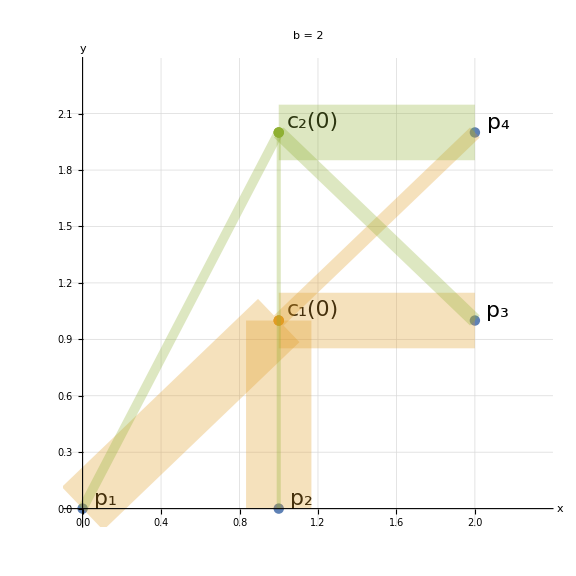

```mathematica
plot[bDefault,0]
```

## Part 1: Re-Assignment Step

One can reduce the number of required calculations by making use of the fact that f_(μ,1)+f_(μ,2)=1.

```mathematica
Table[Subscript[f, bDefault][μ,j],{μ,1,Length[data]},{j,1,Length[cluster]}]//MatrixForm
```

(5/7 | 2/7
4/5 | 1/5
2/3 | 1/3
1/3 | 2/3)

## Part 2: Re-Calculation of the Cluster Centres

Cluster centres of iteration t=1:

```mathematica
calculateClusters[bDefault]
```

{{1.02659,0.390833},{1.69984,1.47669}}

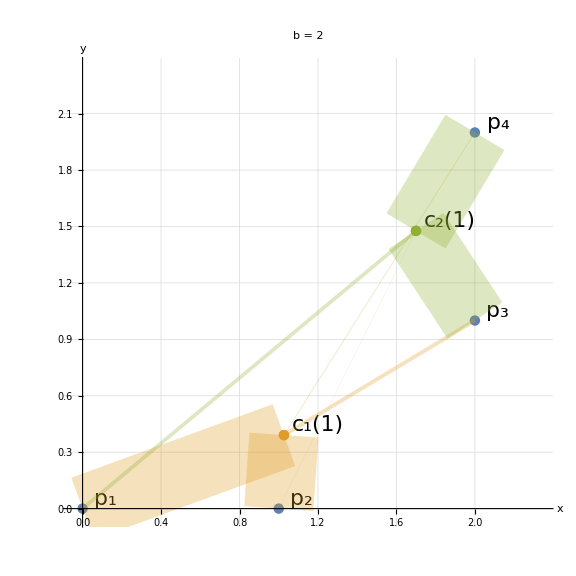

```mathematica
plot[bDefault,1]
```

## Part 3: Cluster Result

Cluster centres of iteration t=100:

```mathematica
Do[
calculateClusters[bDefault];
,{t,2,100}]
```

```mathematica
cluster//N
```

{{0.485528,0.00456674},{1.99543,1.51447}}

The result is nearly the same as in crisp k-means clustering (where we end up with c_1=(0.5,0) and c_2=(2,1.5)).

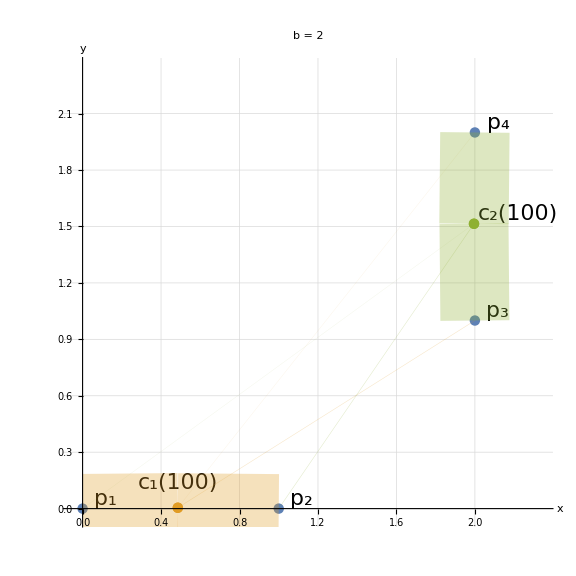

```mathematica
plot[bDefault,100]
```

## Part 4: Fuzzifier b

### Graph Analysis

```mathematica
cluster=clusterInit;
```

Even though the values for f_(1,j) tend to get smaller, we normalize them later with 1/(f_(1,1)^b+f_(1,2)^b) which does work as a counterforce to compensate for the small values.

Regarding the overlap, it does indeed increase for larger values for b (the two dotted lines get closer to each other). This means that the membership is split more between the clusters.

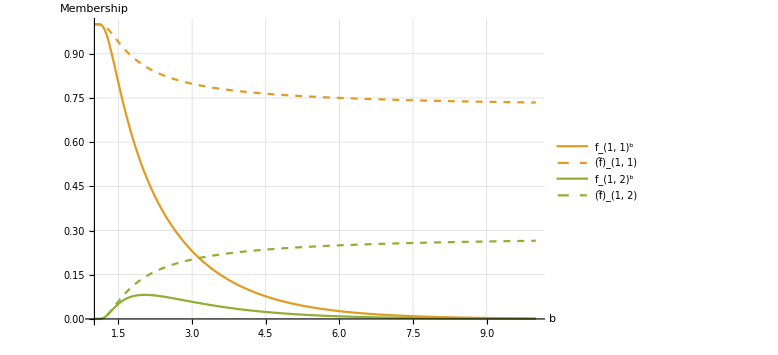

```mathematica
Plot[{(Subscript[f, b][1,1])^b,(Subscript[f, b][1,1])^b/((Subscript[f, b][1,1])^b+(Subscript[f, b][1,2])^b),(Subscript[f, b][1,2])^b,(Subscript[f, b][1,2])^b/((Subscript[f, b][1,1])^b+(Subscript[f, b][1,2])^b)},{b,1.01,10},
PlotTheme->"myTheme",
GridLines->Automatic,
PlotRange->Full,
AxesLabel->{b,"Membership"},
PlotLegends->{"f_(1, 1)^b","(f̃)_(1, 1)","f_(1, 2)^b","(f̃)_(1, 2)"},
PlotStyle->{colorC1,Directive[colorC1,Dashed],colorC2,Directive[colorC2,Dashed]}
]
```

### The Limit lim_(b→1)

The limits give us exact relationships meaning that we basically reduce to crisp k-means.

```mathematica
Limit[(Subscript[f, b][1,1])^b,b->1]
```

1

```mathematica
Limit[(Subscript[f, b][1,2])^b,b->1]
```

0

The critical part is the relationship (e.g. for f_(1,1))

(‖p_1-c_1‖)^2/(‖p_1-c_2‖)^2

If the distance to the first cluster is lower than to the second cluster we get a value <1 and the exponent 1/(b-1)turns it into (basically) 0. Hence, we have 1/(1+0)=1. On the other hand, if the distance to the first cluster is larger than to the second cluster, we have a value >1 and now the exponent turns it into a very large value resulting in lim_(a→∞) 1/(1+a)=0.

### The Limit lim_(b→∞)

```mathematica
f11=1/(1+(Norm[Subscript[p, 1]-Subscript[c, 1]]^2/Norm[Subscript[p, 1]-Subscript[c, 2]]^2)^(1/(b-1)));
f12=1/(1+(Norm[Subscript[p, 1]-Subscript[c, 2]]^2/Norm[Subscript[p, 1]-Subscript[c, 1]]^2)^(1/(b-1)));
```

```mathematica
f11Limit=Limit[f11^b/(f11^b+f12^b),b->∞]
```

Norm[-c_2+p_1]^2/(Norm[-c_1+p_1]^2+Norm[-c_2+p_1]^2)

```mathematica
f12Limit=Limit[f12^b/(f11^b+f12^b),b->∞]
```

Norm[-c_1+p_1]^2/(Norm[-c_1+p_1]^2+Norm[-c_2+p_1]^2)

So, what does it mean? This basically tells us that in the other end of the extreme we take the relationship of the distances from the point to the cluster compared to the distances to all clusters. And as closer a point is to a cluster, as higher the membership is.

```mathematica
f11Limit/.{Subscript[x, 1]->data[[1]],Subscript[c, 1]->cluster[[1]],Subscript[c, 2]->cluster[[2]]}
```

5/7

```mathematica
f12Limit/.{Subscript[x, 1]->data[[1]],Subscript[c, 1]->cluster[[1]],Subscript[c, 2]->cluster[[2]]}
```

2/7

```mathematica
Limit[(Subscript[f, b][1,1])^b/((Subscript[f, b][1,1])^b+(Subscript[f, b][1,2])^b),b->∞]
```

5/7

```mathematica
Limit[(Subscript[f, b][1,2])^b/((Subscript[f, b][1,1])^b+(Subscript[f, b][1,2])^b),b->∞]
```

2/7

All together, the fuzzifier b controls the clustering between two extreme case. From the situation where we end up with crisp membership again to a situation where the result is solely based on the distances.

### Higher Values for b

In the result for b=2 we can see that the memberships are very crisp (two very thick and two very thin lines). If we now increase b, we amplify the overlap of the membership like shown in the previous analysis. This means that the two thin lines get bigger and pull the centroids more to themselves resulting in a situation as shown below.

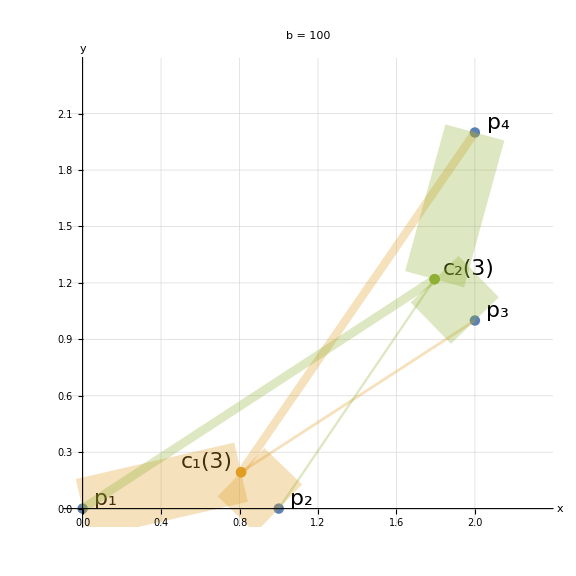

```mathematica
repeatClustering[100]
```

```mathematica
repeatClustering[b_]:=Block[{iterations},
cluster={{1,1},{1,2}};
iterations=3;

Do[
calculateClusters[b];
,{i,1,iterations}];

plot[b,iterations]
]
```

```mathematica
Manipulate[
repeatClustering[bControl],
{bControl,1.1,100}]
```